## Sphere of Influence

```mathematica
SoI[R_,m_,M_]:=R(m/M)^(2/5)
```

#### SoI - Moon vs. Earth

```mathematica
SoI[
Entity["PlanetaryMoon","Moon"][EntityProperty["PlanetaryMoon","DistanceFromEarth"]],
Entity["PlanetaryMoon","Moon"][EntityProperty["PlanetaryMoon","Mass"]],
Entity["Planet","Earth"][EntityProperty["Planet","Mass"]]]
```

65762.1 km

#### SoI - Earth vs. Sun

```mathematica
UnitConvert[SoI[
Entity["Star","Sun"][EntityProperty["Star","DistanceFromEarth"]],
Entity["Planet","Earth"][EntityProperty["Planet","Mass"]],
Entity["Star","Sun"][EntityProperty["Star","Mass"]]],"Kilometers"]
```

911441. km

#### SoI - Moon vs. Sun

```mathematica
UnitConvert[SoI[
Entity["Star","Sun"][EntityProperty["Star","DistanceFromEarth"]],
Entity["PlanetaryMoon","Moon"][EntityProperty["PlanetaryMoon","Mass"]],
Entity["Star","Sun"][EntityProperty["Star","Mass"]]],"Kilometers"]
```

156928. km

## Hill Sphere

```mathematica
HillSphere[a_,m_,M_]:=a(m/(3M))^(1/3)
```

#### Hill - Moon vs. Earth

```mathematica
HillSphere[
Entity["PlanetaryMoon","Moon"][EntityProperty["PlanetaryMoon","DistanceFromEarth"]],
Entity["PlanetaryMoon","Moon"][EntityProperty["PlanetaryMoon","Mass"]],
Entity["Planet","Earth"][EntityProperty["Planet","Mass"]]]
```

61219.4 km

#### Hill - Earth vs. Sun

```mathematica
UnitConvert[
HillSphere[
Entity["Star","Sun"][EntityProperty["Star","DistanceFromEarth"]],
Entity["Planet","Earth"][EntityProperty["Planet","Mass"]],
Entity["Star","Sun"][EntityProperty["Star","Mass"]]],"Kilometers"]
```

1.47518×10^6 km

#### Hill - Moon vs. Sun

```mathematica
UnitConvert[HillSphere[
Entity["Star","Sun"][EntityProperty["Star","DistanceFromEarth"]],
Entity["PlanetaryMoon","Moon"][EntityProperty["PlanetaryMoon","Mass"]],
Entity["Star","Sun"][EntityProperty["Star","Mass"]]],"Kilometers"]
```

340524. km

```mathematica
rules={
m->Entity["PlanetaryMoon","Moon"][EntityProperty["PlanetaryMoon","Mass"]],M->Entity["Planet","Earth"][EntityProperty["Planet","Mass"]]};
```

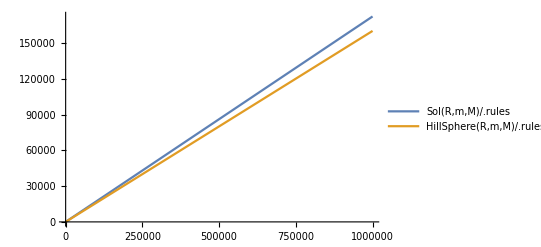

```mathematica
Plot[
{SoI[R,m,M]/.rules,
HillSphere[R,m,M]/.rules},
{R,0,Quantity[1 10^6, "Kilometers"]},PlotLegends->"Expressions"]
```

### When are SoI and Hill equal? (Earth and moon)

```mathematica
Solve[(x)^(2/5)==(x/3)^(1/3),x]
```

{{x→0},{x→1/243}}

```mathematica
{%[[2]]//N,Entity["PlanetaryMoon","Moon"][EntityProperty["PlanetaryMoon","Mass"]]/Entity["Planet","Earth"][EntityProperty["Planet","Mass"]]//N,Entity["Planet","Earth"][EntityProperty["Planet","Mass"]]/Entity["Star","Sun"][EntityProperty["Star","Mass"]]//N
}
```

{{x→0.00411523},0.0123002,3.00347×10^-6}

```mathematica
rules={R->Entity["PlanetaryMoon","Moon"][EntityProperty["PlanetaryMoon","DistanceFromEarth"]],M->Entity["Planet","Earth"][EntityProperty["Planet","Mass"]]};
```

```mathematica
Plot[
{SoI[R,m,M]/.rules,
HillSphere[R,m,M]/.rules},
{m,Quantity[0, "Kilograms"],Quantity[0.01, "EarthMass"]},PlotLegends->"Expressions"]
```

-Graphics-

### When are SoI and Hill equal? (Sun and Earth)

```mathematica
rules={R->Entity["Planet","Earth"][EntityProperty["Planet","AverageOrbitDistance"]],M->Entity["Star","Sun"][EntityProperty["Star","Mass"]]};
```

```mathematica
Plot[
{SoI[R,m,M]/.rules,
HillSphere[R,m,M]/.rules},
{m,Quantity[0, "Kilograms"],10*Entity["Planet","Jupiter"][EntityProperty["Planet","Mass"]]},PlotLegends->"Expressions"]
```

-Graphics-

## Distance of equal force in 3 body system?

```mathematica
Solve[M1/r^2==M2/(a-r)^2,r]//Simplify
```

{{r→(a √M1)/(√M1+√M2)},{r→(a √M1)/(√M1-√M2)}}

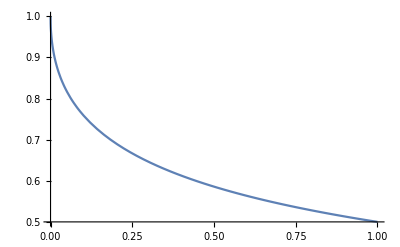

```mathematica
Plot[Evaluate[(a √M1)/(√M1+√M2)/.{a->1,M1->1}],{M2,0,1}]
```

```mathematica
Entity["Planet","Earth"][EntityProperty["Planet","Mass"]]/(Entity["PlanetaryMoon","Moon"][EntityProperty["PlanetaryMoon","DistanceFromEarth"]]-Entity["PlanetaryMoon","Moon"][EntityProperty["PlanetaryMoon","Radius"]]-Quantity[100, "Kilometers"])^2*(Entity["PlanetaryMoon","Moon"][EntityProperty["PlanetaryMoon","Radius"]]+Quantity[100, "Kilometers"])^2/(Entity["PlanetaryMoon","Moon"][EntityProperty["PlanetaryMoon","Mass"]])
```

0.00189401